```mathematica
tf=10;
sol=NDSolve[{x1''[t]==Sin[x2[t]-x1[t]],x2''[t]==-Sin[x2[t]-x1[t]],x1'[0]==-1,x2'[0]==0,x1[0]==0,x2[0]==Pi},{x1,x2},{t,0,tf}];
s1= x1  /. First@sol;
s2= x2 /. First@sol;
Animate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```

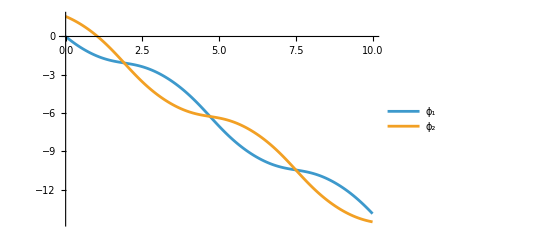

```mathematica
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All]]
```

```mathematica
Export["~/Desktop/Classical/Presentation Problem 2/fig3.png",Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All,AxesLabel->{"t", "ϕ"}]],ImageResolution->300]
```

~/Desktop/Classical/Presentation Problem 2/fig3.png

```mathematica
tf=10;
s=NDSolve[{x1''[t]==Sin[x2[t]-x1[t]],x2''[t]==-Sin[x2[t]-x1[t]],x1'[0]==0,x2'[0]==0.1,x1[0]==0,x2[0]==Pi},{x1,x2},{t,0,tf}];
s11= x1  /. First@s;
s12= x2 /. First@s;
Animate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],ListLinePlot[{{Cos[s11[t]],Sin[s11[t]]},{Cos[s12[t]],Sin[s12[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s11[t]],Sin[s11[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s12[t]],Sin[s12[t]]}]}]],{t,0,tf}]
```

```mathematica
Animate[Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}],ListLinePlot[{{0,0},{Cos[s1[t]],Sin[s1[t]]}},PlotStyle->{RGBColor[0.394, 0.394, 0.394],Dashed}],ListLinePlot[{{0,0},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{RGBColor[0.668, 0.668, 0.668],Dashed}],ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```